```mathematica
Clear["Global`*"]
```

```mathematica
J1=2;
E0=-3*B/2;
E1=(-B-J2)/2;
E2=(B-J2)/2;
E3=-B/2+1/4*(J2-Sqrt[J2^2+8*J1^2]);
E4=B/2+1/4*(J2-Sqrt[J2^2+8*J1^2]);
E5=-B/2+1/4*(J2+Sqrt[J2^2+8*J1^2]);
E6=B/2+1/4*(J2+Sqrt[J2^2+8*J1^2]);
E7=3*B/2;
a3=a4=(-J2-Sqrt[J2^2+8*J1^2])/(2*J1);
a5=a6=Sqrt[2+a4^2];
N3=N4=Sqrt[2+a3^2];
N5=N6=Sqrt[2+a6^2];
T=0.05;
u=Exp[-E0/T]+((a3^2)*Exp[-E3/T]/(N3^2))+(a5^2)*Exp[-E5/T]/(N5^2);
v=Exp[-E7/T]+((a4^2)*Exp[-E4/T]/(N4^2))+(a6^2)*Exp[-E6/T]/(N6^2);
w=-1/2*Exp[-E1/T]-1/2*Exp[-E2/T]+(Exp[-E3/T]/(N3^2))+(Exp[-E4/T]/(N4^2))+(Exp[-E5/T]/(N5^2))+(Exp[-E6/T]/(N6^2));
Z=Exp[3 B/(2 T)]+Exp[(B+J2)/(2 T)]+Exp[(-B+J2)/(2 T)]+Exp[(2 B-(J2-Sqrt[J2^2+8*J1^2]))/(4 T)]+Exp[-(2 B+(J2-Sqrt[J2^2+8*J1^2]))/(4 T)]+Exp[(2 B-(J2+Sqrt[J2^2+8*J1^2]))/(4 T)]+Exp[-(2 B+(J2+Sqrt[J2^2+8*J1^2]))/(4 T)]+Exp[-3 B/(2 T)];
C1=2*(Abs[w]-Sqrt[u*v])/Z;
C2=Max[C1,0];
Plot3D[C2,{J2,-8,8},{B,-8,8}]
```

-Graphics3D-

```mathematica
Plot3D[C2,{J2,-8,8},{B,-8,8},Ticks->{{-8,-4,0,4,8},{-8,-4,0,4,8},{0,0.5,1}}]
```

-Graphics3D-

```mathematica
ContourPlot[C2,{B,-8,8},{J2,-8,8},ContourShading->None,ContourStyle->Black]
```

-Graphics-

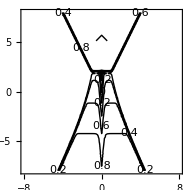

```mathematica
ContourPlot[C1,{B,-8,8},{J2,-8,8},ContourShading->None,ContourStyle->Black,ContourLabels->True
]
```

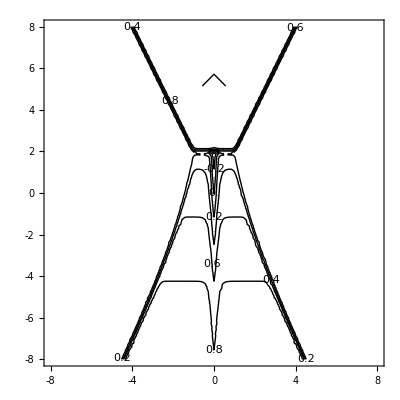

```mathematica
ContourPlot[C1,{B,-8,8},{J2,-8,8},ContourShading->None,ContourStyle->Black,ContourLabels->True,Frame->True,FrameTicks->{{{-8,-6,-4,-2,0,2,4,6,8},None},{{-8,-6,-4,-2,0,2,4,6,8},None}}]
```